# Задание 01.

## Знакомство с системой Wolfram Mathematica

## Мосейков Игнатий Геннадьевич, гр. №21372

Что больше π^ⅇ или ⅇ^π?

```mathematica
If [Pi^Exp[1]>Exp[Pi], Pi^Exp[1], Exp[Pi]]
```

ⅇ^π

Вычислить √3 - ln(2) с точностью 20 знаков после запятой

```mathematica
NumberForm[N[√3-Log[2]],20]
```

1.038903627008932

Постройте графики (Plot, PlotStyle, PlotRange, AxesLabel, PlotLabel) так, чтобы

- функций tan(x), sin(x) и cos(x) были на одном рисунке в интервале x∈[-8,8]

- sin(x) отображался красной сплошной линией, cos(x) - синей пунктирной, tan(x) — зелеными точками,

- диапазон по оси y∈[-3,3].

- появились подписи к осям

- отобразилось названия графика

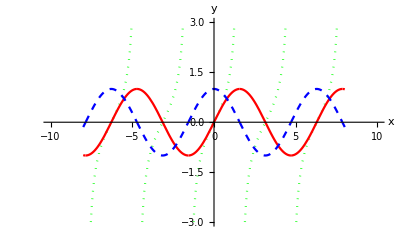

```mathematica
Plot[{Tan[x], Sin[x], Cos[x]}, {x,-8,8},PlotRange->{{-10,10},{-3,3}}, PlotStyle->{{Dotted, Green},{Red}, {Dashed, Blue}}, AxesLabel->{x,y}]
```

Для параметра a=0.1 нарисуйте график спирали в полярных координатах: r(ϕ)=ⅇ^(a ϕ), где ϕ∈[0,6π]  с помощью функции PolarPlot. 
Постройте тот же график, используя параметрическое описание спирали в декартовых координатах x(ϕ), y(ϕ) с помощью  функции ParametricPlot.

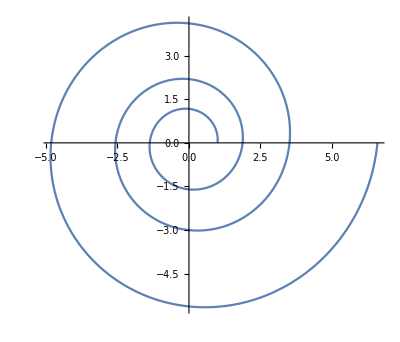

```mathematica
a = 0.1;
PolarPlot[Exp[a*t],{t,0,6*Pi}]
```

```mathematica
ParametricPlot[{Exp[a*t]*Cos[t], Exp[a*t]*Sin[t]}, {t,0,6*Pi}]
```

-Graphics-

Постройте трехмерный график функции f(x,y)=(sin(r))/r,r=√(x^2+y^2), в области x,y∈[-10,10]. Добейтесь того, чтобы график помещался на рисунке. (Plot3D)

```mathematica
r = Sqrt[x^2 + y^2];
Plot3D[Sin[r]/r, {x,-10,10},{y,-10, 10}, PlotRange->All]
```

-Graphics3D-

С помощью параметрического задания поверхности нарисуйте тор. (ParametricPlot3D)

```mathematica
R = 3;
r = 1;
ParametricPlot3D[{(r*Sin[t]-R)*Cos[u],(r*Sin[t]-R)*Sin[u],r*Cos[t]},{t,-Pi,Pi},{u,0,2*Pi}]
```

-Graphics3D-

Дан список data из экспериментальных пар значений {x,f(x)}. С помощью функции Fit найдите аппроксимирующие функции

в виде полинома второй степени от x

в виде линейной комбинации  sin(x) и cos(x)

затем постройте на одном графике экспериментальные точки и аппроксимирующие функции. (Show, ListPlot, Fit)

```mathematica
data={{0., 0.58}, {0.4, 1.39}, {0.8, 1.77}, {1.2, 2.12}, {1.6, 2.10},{2.,1.55}, {2.4, 1.14}, {2.8,0.48}, {3.2,-0.24}, {3.6,-1.24}, {4.,-1.59}};
```

0.841538+1.49653 x-0.553904 x^2

0.374044 Cos[x]+2.05184 Sin[x]

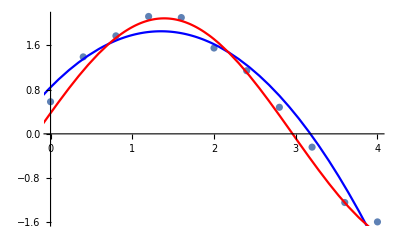

```mathematica
first = Fit[data, {1,x,x^2},x]
second = Fit[data, {Sin[x],Cos[x]},x]
Show[ListPlot[data],Plot[{first,second},{x,-1, 5}, PlotStyle->{Blue, Red}]]
```

Вывести списком несколько первых функций Бесселя J_(n+1/2)(x) . Найти разложение J_(n+1/2)(x) при малых x→0 и больших x→∞ до первого неисчезающего члена. (Table, Bessel*, Series, Normal)

```mathematica
Table[BesselJ[i+1/2,x],{i,0,3}]
Normal[Series[BesselJ[i+1/2,x],{x,0,10}]]
Normal[Series[BesselJ[i+1/2,x],{x,∞,3}]]
```

{(√(2/π) Sin[x])/(√x),(√(2/π) (-Cos[x]+Sin[x]/x))/(√x),(√(2/π) (-(3 Cos[x])/x-Sin[x]+(3 Sin[x])/x^2))/(√x),(√(2/π) (Cos[x]-(15 Cos[x])/x^2+(15 Sin[x])/x^3-(6 Sin[x])/x))/(√x)}

x^i ((2^(-1/2-i) √x)/Gamma[3/2+i]-(2^(-5/2-i) x^(5/2))/((3/2+i) Gamma[3/2+i])+(2^(-11/2-i) x^(9/2))/((3/2+i) (5/2+i) Gamma[3/2+i])-(2^(-15/2-i) x^(13/2))/(3 (3/2+i) (5/2+i) (7/2+i) Gamma[3/2+i])+(2^(-23/2-i) x^(17/2))/(3 (3/2+i) (5/2+i) (7/2+i) (9/2+i) Gamma[3/2+i]))

(-((-1+i) i (1+i) (2+i))/(4 √(2 π) x^(5/2))+(√(2/π))/(√x)) Cos[1/2 (1+i) π-x]+((i+i^2) Sin[1/2 (1+i) π-x])/(√(2 π) x^(3/2))

С помощью Mathematica определите нормировочный коэффициент для волновой функции электрона в атоме водорода ψ_200(r,θ,ϕ) =A ⅇ^(-r/2a)(1-r/(2a)), где a — константа, обозначающая боровский радиус. (Integrate, Assumptions, Solve, Rule)

```mathematica
Clear[a];
Clear[r];
Solve[Refine[Integrate[(A*Exp[-r/(2*a)]*(1-r/(2*a)))^2,{r,0,Infinity},{u,0,2*Pi},{v,-Pi, Pi}],Assumptions->{a>0, a<1}]==1,A]
```

{{A→-1/(√2 √a π)},{A→1/(√2 √a π)}}